```mathematica
(*Directory to save files, change if needed *)SetDirectory["/Users/George/Documents/"];
```

```mathematica
kmin=10^(-3);
kmax=20;
```

```mathematica
Clear[rval]
```

```mathematica
rval=1;
xval=0.1;
amin=0.002;
amax=1;
```

```mathematica
(*Background cosmology - change to yours*)
```

```mathematica
Om=0.281;
```

```mathematica
adot=Sqrt[Om /a+(1-Om)a*a];
```

```mathematica
intToday=Assuming[ Int∈Reals ,Integrate[1/(adot^3),{a,0,amin}]];
```

```mathematica
H=adot/a;
```

```mathematica
Clear[H1]
```

```mathematica
H1=(H)/.a->amin
```

5926.63

```mathematica
Clear[D1]
```

```mathematica
D1=2.5 Om H1 intToday
```

0.002

```mathematica
H0=H/.a->amax
```

1.

```mathematica
Clear[DH1]
```

```mathematica
DH1=D[(H),a];
```

```mathematica
DH1=DH1/.a->amin
```

-4.44498×10^6

```mathematica
Clear[adotpast]
```

```mathematica
adotpast=adot/.a->amin;
```

```mathematica
Clear[der]
```

```mathematica
der=2.5 Om (DH1*intToday+H1/(adotpast^3))
```

1.

```mathematica
(*Introducing nDGP parameter n=H0*r_c={1,5} *)
```

```mathematica
Clear[n]
```

```mathematica
n=1;
```

```mathematica
c=2997;
```

```mathematica
(*Defining mass term m1 in nDGP, m1=0 for our model. *)
```

```mathematica
Clear[m]
```

```mathematica
m[a_]=0
```

0

```mathematica
Ddot=D[adot,a];
```

```mathematica
Clear[s]
```

```mathematica
s=NDSolve[{(adot^2)* y''[a]+(adot*Ddot+2 adot H) y'[a]==(1.5*(Om/(Om+(1-Om) a^3)))(adot/a)^2  y[a],y'[amin]==der,y[amin]==D1},y,{a,amin,amax},AccuracyGoal->13,PrecisionGoal->20];
```

```mathematica
Clear[lot]
```

```mathematica
lot=D[Evaluate[y[a]/.First@s],a];
```

```mathematica
valtoday = Evaluate[y[a]/.First@s]/.a->amax//N;
```

```mathematica
(*Introduce functions for nDGP model *)
```

```mathematica
Clear[betaDGP]
```

```mathematica
betaDGP[a_]=1+2 n H(1+D[H,a] adot/(3 H H));
```

```mathematica
Clear[beta]
```

```mathematica
beta[a_]=Sqrt[1/(6 betaDGP[a])];
```

```mathematica
Clear[geff]
```

```mathematica
geff[a_]=2 (beta[a])^2;
```

```mathematica
Clear[Eqn]
```

```mathematica
Eqn[a_]= D[p[a],a,a]+(adot*Ddot+2 (adot^2)/a)D[p[a],a]/(adot^2)==(1.5*Om /(a^3))  p[a](1+geff[a])/(adot^2);
```

```mathematica
Clear[del]
```

```mathematica
del[a_]:=Evaluate[y[a]/.First@s]
```

```mathematica
Clear[jk]
```

```mathematica
jk[a_]=D[del[a],a];
```

```mathematica
Clear[dgrowth]
```

```mathematica
(*growing mode *)
```

```mathematica
Clear[soln1]
```

```mathematica
soln1=NDSolve[{Eqn[a],p[amin]==del[amin],Derivative[1][p][amin]==jk[amin]},p[a],{a,amin,amax},Method->"ExplicitRungeKutta"]
```

{{p[a]→InterpolatingFunction[…][a]}}

```mathematica
dgrowth[a_]:=Evaluate[p[a]/.First@soln1]
```

```mathematica
Clear[dergrowth]
```

```mathematica
dergrowth[a_]=D[dgrowth[a],a]
```

InterpolatingFunction[…][a]

```mathematica
Plot[(dgrowth[a])/del[a],{a,0.01,1}];
```

```mathematica
Clear[Afact]
```

```mathematica
Afact[a_]=((1.5*Om /(a^3)))(1+geff[a]);
```

```mathematica
K2fl[k_,r_,x_,a_]=0;
```

```mathematica
Clear[Ppi]
```

```mathematica
Ppi[k_,a_]=k^2/(6 beta[a]^2 a^2);
```

```mathematica
(*Mass factor M2 for [p,k-p] configuration. M3=0 for this model *)
M2[k_,r_,x_,a_]=2 (n^2)k^4 r^2/(a^4)(1-x^2)
```

(2 k^4 r^2 (1-x^2))/a^4

```mathematica
(*Source factor for [p,k-p] configuration *)
```

```mathematica
Clear[Source]
```

```mathematica
Source[k_,r_,x_,a_]=Afact[a]dgrowth[a]dgrowth[ a]-((x^2+r^2-2r x)/(1+r^2-2r x))(Afact[a])dgrowth[a]dgrowth[ a]-(2 ((1.5*Om /(a^3))) k/(3 a))^2 M2[k,r,x,a] dgrowth[a]dgrowth[ a]/(6 Ppi[k,a] Ppi[k r,a] Ppi[k Sqrt[1+r^2-2r x], a]);
```

```mathematica
(*Solve for 2nd order ΛCDM growth factor, in case needed*)
```

```mathematica
dsecond[a_]:=-(3/7) (Om/(Om+(1-Om) a^3))^(-1/143)(del[a]/valtoday)^2
```

```mathematica
bound[a_]:=-(3/7)(Om/(Om+(1-Om) a^3))^(-1/143)(del[a])^2
```

```mathematica
derop2[a_]=D[bound[a],a];
```

```mathematica
s2=NDSolve[{(adot^2)* yy''[a]+(adot*Ddot+2 adot H) yy'[a]==(1.5*Om /(a^3))  (yy[a]-(del[a] )^2),yy[amin]==bound[amin],yy'[amin]==derop2[amin]},yy,{a,amin,amax}];
```

```mathematica
dgrowth2=Evaluate[yy[a]/.First@s2]
```

InterpolatingFunction[…][a]

```mathematica
secondgr[a_]=dgrowth2
```

InterpolatingFunction[…][a]

```mathematica
Clear[Dsecondgr]
```

```mathematica
Dsecondgr[a_]=D[secondgr[a],a]
```

InterpolatingFunction[…][a]

```mathematica
(*Differential equation that gives D(2)[p,k-p]*)
```

```mathematica
Clear[Eqn2]
```

```mathematica
Eqn2[k_,r_,x_,a_]= D[pk[a],a,a]+(adot*Ddot+2 (adot^2)/a)D[pk[a],a]/(adot^2)==(Afact[a]pk[a]+ Source[k,r,x,a])/(adot^2);
```

```mathematica
(*Eqn2= D[pk[k,a],a,a]+(adot*Ddot+2 adot H)D[pk[k,a],a]/(adot^2)==(Afact[k,a]pk[k,a]+(Afact[k,a]dgrowth[k ,a]dgrowth[k , a]))/(adot^2);
```

```mathematica
Clear[nsolsecond]
```

```mathematica
nsolsecond[k_?NumericQ,r_,x_]:=First[pk[a]/.NDSolve[{Eqn2[k,r,x,a],pk[amin]==- secondgr[amin](1-(x^2+r^2-2r x)/(1+r^2-2r x)),Derivative[1][pk][amin]==- Dsecondgr[amin](1-(x^2+r^2-2r x)/(1+r^2-2r x)) },pk[a],{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]]
```

```mathematica
Clear[D2growth]
```

```mathematica
D2growth[k_,r_,x_,anew_]:=nsolsecond[k,r,x]/.a->anew
```

```mathematica
(*K2fl factor for [p,k] configuration *)
```

```mathematica
Clear[K2flpk]
```

```mathematica
K2flpk[k_,r_,x_,a_]=0;
```

```mathematica
(*Source factor for [p,k] configuration *)
```

```mathematica
Clear[Sourcepk]
```

```mathematica
Sourcepk[k_,r_,x_,a_]=Afact[ a]dgrowth[a]dgrowth[a]-(x^2)(Afact[a])dgrowth[a]dgrowth[ a]-(2 ((1.5*Om /(a^3)))k Sqrt[1+r^2+2r x]/(3 a))^2 M2[k,r,x,a] dgrowth[a]dgrowth[ a]/(6 Ppi[k,a] Ppi[k r,a] Ppi[k Sqrt[1+r^2+2r x], a]);
```

```mathematica
(*Differential equation that gives D(2)[p,k]*)
```

```mathematica
Clear[Eqndif2]
```

```mathematica
Eqndif2[k_,r_,x_,a_]= D[pkdif[ a],a,a]+(adot*Ddot+2 (adot^2)/a)D[pkdif[ a],a]/(adot^2)==((Afact[a]pkdif[ a])+ Sourcepk[k,r,x,a])/(adot^2);
```

```mathematica
(*nsolseconddif=NDSolve[{Eqndif2,pkdif[k,amin]==-secondgr[amin],pkdif^(0,1)[k,amin]==-Dsecondgr[amin]},pkdif[k,a],{k,kmin,kmax},{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]
```

```mathematica
Clear[nsolseconddif]
```

```mathematica
nsolseconddif[k_?NumericQ,r_,x_]:=First[pkdif[a]/.NDSolve[{Eqndif2[k,r,x,a],pkdif[amin]==-secondgr[amin](1-x^2),Derivative[1][pkdif][amin]==-Dsecondgr[amin](1-x^2)},pkdif[a],{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]]
```

```mathematica
(* D(2)[p,k]*)
```

```mathematica
Clear[D2pk]
```

```mathematica
D2pk[k_,r_,x_,anew_]:=nsolseconddif[k,r,x]/.a->anew
```

```mathematica
Clear[der2pk]
```

```mathematica
der2pk[k_,r_,x_,anew_]:=D[nsolseconddif[k,r,x],a]/.a->anew
```

```mathematica
derder2pk[k_,r_,x_,anew_]:=D[nsolseconddif[k,r,x],a,a]/.a->anew
```

```mathematica
(*testing stuff*)
```

```mathematica
(*D2φ factor for [p,k] configuration *)
```

```mathematica
Clear[D2phi]
```

```mathematica
D2phi[k_,r_,x_,a_]:=D2pk[k,r,x,a] +(1+x^2) dgrowth[a] dgrowth[a]-(2 ((1.5*Om /(a^3)))/3) (M2[k,r,x,a])/(3 Ppi[k ,a] Ppi[k r,a]) dgrowth[a] dgrowth[a];
```

```mathematica
(*3rd Mass factor for configurations *)
M3kpp[k_,r_,x_,a_]= 3(n^2)k^6 r^3 x/(a^6 beta[a]^2 ((1.5*Om /(a^3))))(x-1);
```

```mathematica
M3ppk[k_,r_,x_,a_]=3(n^2)k^6 r^4 /(a^6 beta[a]^2 ((1.5*Om /(a^3))))(1-x^2);
```

```mathematica
Clear[K3rd]
```

```mathematica
(*K(3)_δI screening factor that will be used for source term below*)
K3rd[k_,r_,x_,a_]:=
(1/6)  (2 ((1.5*Om /(a^3)))/3)^3 ( M3kpp[k,r,x,a]/(Ppi[k,a] Ppi[k r,a]^2))+(1/6) ((2 ((1.5*Om /(a^3)))/3)^2 3 M2[k,r,x,a] (1+x^2+D2pk[k,r,x,a]/(dgrowth[a] dgrowth[a]))/(Ppi[k r,a]Ppi[k Sqrt[1+r^2+2r x],a])+ (2 ((1.5*Om /(a^3)))/3)^3  (M3ppk[k,r,x,a]/(Ppi[k,a] Ppi[k r,a]^2)-M2[k,r,x,a] (M2[k,r,x,a] )/(Ppi[k Sqrt[1+r^2+2r x],a] Ppi[k,a] Ppi[k r,a]^2)))+(1./6) ((2 ((1.5*Om /(a^3)))/3)^2 3 M2[k,r,x,a] (1+x^2+D2pk[k,-r,x,a]/(dgrowth[a] dgrowth[a]))/(Ppi[k r,a]Ppi[k Sqrt[1+r^2-2r x],a])+ (2 ((1.5*Om /(a^3)))/3)^3  (- M2[k,r,x,a] (M2[k,r,x,a] )/(Ppi[k Sqrt[1+r^2-2r x],a] Ppi[k,a] Ppi[k r,a]^2)))
```

```mathematica
(*Source factor for D(3)[k,-p,p] differential equation *)
```

```mathematica
Clear[Source3rd]
```

```mathematica
Source3rd[k_,r_,x_,a_]:=dgrowth[a]((Afact[a]-Afact[a])D2pk[k,r,x,a]+adot^2 derder2pk[k,r,x,a]+(adot*Ddot+2 (adot^2)/a)der2pk[k,r,x,a] ) (1-x^2)/(1+r^2+2r x)+((2 ((1.5*Om /(a^3))) k Sqrt[1+r^2+2r x]/(3 a))^2M2[k,r,x,a]/(6 Ppi[k ,a] Ppi[k r,a] Ppi[k Sqrt[1+r^2+2r x], a]))(dgrowth[a])^2 dgrowth[a]- (1/2)(k^2/a^2)/(6 Ppi[k,a]) K3rd[k,r,x,a] dgrowth[a] dgrowth[a]^2 ;
```

```mathematica
Clear[Source3rdsym]
```

```mathematica
Source3rdsym[k_,r_,x_,a_]:= (Source3rd[k,r,x,a]+Source3rd[k,-r,x,a]);
```

```mathematica
Clear[Eqn3d]
```

```mathematica
Eqn3d[k_,r_,x_,a_]:= D[pk3d[a],a,a]+(adot*Ddot+2 (adot^2)/a)D[pk3d[a],a]/(adot^2)==(Afact[a]pk3d[a]+ Source3rdsym[k,r,x,a])/(adot^2);
```

```mathematica
(*nsol3d=NDSolve[{Eqn3d,pk3d[k,amin]==-secondgr[amin],pk3d^(0,1)[k,amin]==-Dsecondgr[amin]},pk3d[k,a],{k,kmin,kmax},{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]
```

```mathematica
D3LCDM[a_]=(5/7)(del[a])^3;
```

```mathematica
Der3LCDM[a_]=D[D3LCDM[a],a];
```

```mathematica
Clear[nsol3d]
```

```mathematica
nsol3d[k_?NumericQ,r_,x_]:=First[pk3d[a]/.NDSolve[{Eqn3d[k,r,x,a],pk3d[amin]==(2/3)D3LCDM[amin] (1-x^2)^2/(1+r^2-2 r x),Derivative[1][pk3d][amin]==(2/3)Der3LCDM[amin] (1-x^2)^2/(1+r^2-2 r x) },pk3d[a],{a,amin,amax},PrecisionGoal->20,AccuracyGoal->13]]
```

```mathematica
Clear[D3symgrowth]
```

```mathematica
D3symgrowth[k_,r_,x_,anew_]:=nsol3d[k,r,x]/.a->anew
```

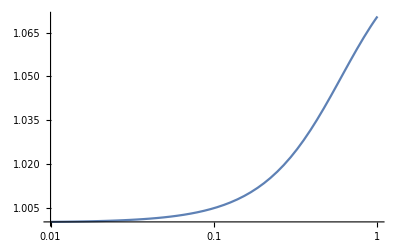

```mathematica
(*The code has now calculated the 1st, 2nd and 3rd order growth factors that are needed for calculating the CLPT statistics in nDGP MG gravity. As explained in the paper, the 1st order growth factor for MG is a function of time a only (unlike f(R)). Here it is given by the function dgrowth[a]. The 2nd and 3rd order growth factors are functions of k, r, x and a and are given by D2pk[k,r,x,a], D2growth[k,r,x,a] and D3symgrowth[k,r,x,a].
D2pk and D2growth are the 2 different configurations, D2(p,k) and D2(p,k-p]) that we need for CLPT.
Plotting all of these below vs r, for k=1, x=0.05 and a=1. 
D1[a] is plotted as a function of time instead.
del[a] is the LCDM linear growth factor. *)
LogLinearPlot[dgrowth[a]/del[a],{a,0.01, 1}]
```

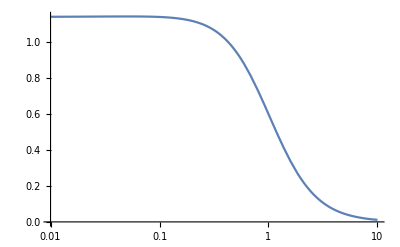

```mathematica
LogLinearPlot[(7/3)D2growth[1,r,0.05,1]/(del[1] del[1]),{r,0.01, 10}]
```

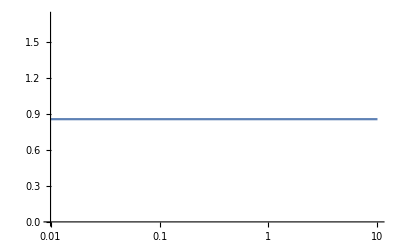

```mathematica
LogLinearPlot[(7/3)D2pk[1,r,0.5,1]/(del[1] del[1]),{r,0.01, 10}]
```

```mathematica
(*End of growth factor calculation section *)
```